```mathematica
n = 1;ys = Range[200];While[True,
Values1={V->2,α->.1,β->.5,y-> n/10,δ->5};
Deposit[ψ_,R_,Values1_]:=1-CDF[NormalDistribution[0,1],α/(√β) (ψ-y+R (√(α+β))/α)+√β (ψ-θ)]/.Values1;
BankPayoff[ψ_,R_,Values1_]:=((V-1/CDF[NormalDistribution[0,1],R]) /.Values1)NIntegrate[Deposit[ψ,R,Values1] PDF[NormalDistribution[y,√(1/α)]/.Values1,θ],{θ,ψ,+∞}];
Rs =NArgMax[{
ψtemp=ψ/.FindRoot[ψ==((δ CDF[NormalDistribution[0,1],(α/(√β) (ψ-y+R (√(α+β))/α))/.Values1])/.Values1),{ψ,10}];
BankPayoff[ψtemp,R,Values1]
},{R,0.01,10}];
r = 1/CDF[NormalDistribution[0,1],Rs];
ys[[n]] = r;
Print["x:",n/10," ,y:",r];
If[n==200, Break[]];
n++;
]
```

FindRoot::nlnum: The function value {10.-2.5 Erfc[-0.1 (9.9+7.74597 R)]} is not a list of numbers with dimensions {1} at {ψ} = {10.}.

ReplaceAll::reps: {FindRoot[ψ==(δ CDF[NormalDistribution[0,1],Times[«2»]/.Values1]/.Values1),{ψ,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {10.-2.5 Erfc[-0.1 (9.9+7.74597 R)]} is not a list of numbers with dimensions {1} at {ψ} = {10.}.

ReplaceAll::reps: {FindRoot[ψ==(δ CDF[NormalDistribution[0,1],Times[«2»]/.Values1]/.Values1),{ψ,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {10.-2.5 Erfc[-0.1 (9.9+7.74597 R)]} is not a list of numbers with dimensions {1} at {ψ} = {10.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ψ==(δ CDF[NormalDistribution[0,1],Times[«2»]/.Values1]/.Values1),{ψ,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand 0.126157 ⅇ^(-0.05 (-1/10+θ)^2) (1-1/2 Erfc[(-0.141421 Plus[«3»]-0.707107 Plus[«2»])/(√2)]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.+(ψ/.FindRoot[ψ==(Times[«2»]/.Values1),{ψ,10.}])}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

x:1/10 ,y:1.52677

x:1/5 ,y:1.52521

x:3/10 ,y:1.52357

x:2/5 ,y:1.52184

x:1/2 ,y:1.52002

x:3/5 ,y:1.51811

x:7/10 ,y:1.51611

x:4/5 ,y:1.51401

x:9/10 ,y:1.51181

x:1 ,y:1.50951

x:11/10 ,y:1.50711

x:6/5 ,y:1.50461

x:13/10 ,y:1.50199

x:7/5 ,y:1.49928

x:3/2 ,y:1.49645

x:8/5 ,y:1.49351

x:17/10 ,y:1.49047

x:9/5 ,y:1.48731

x:19/10 ,y:1.48403

x:2 ,y:1.48065

x:21/10 ,y:1.47714

x:11/5 ,y:1.47353

x:23/10 ,y:1.4698

x:12/5 ,y:1.46596

x:5/2 ,y:1.462

x:13/5 ,y:1.45793

x:27/10 ,y:1.45375

x:14/5 ,y:1.44946

x:29/10 ,y:1.44506

x:3 ,y:1.44055

x:31/10 ,y:1.43593

x:16/5 ,y:1.43121

x:33/10 ,y:1.42639

x:17/5 ,y:1.42147

x:7/2 ,y:1.41645

x:18/5 ,y:1.41134

x:37/10 ,y:1.40614

x:19/5 ,y:1.40085

x:39/10 ,y:1.39547

x:4 ,y:1.39002

x:41/10 ,y:1.38449

x:21/5 ,y:1.37889

x:43/10 ,y:1.37321

x:22/5 ,y:1.36748

x:9/2 ,y:1.36168

x:23/5 ,y:1.35583

x:47/10 ,y:1.34993

x:24/5 ,y:1.34399

x:49/10 ,y:1.338

x:5 ,y:1.33197

x:51/10 ,y:1.32592

x:26/5 ,y:1.31984

x:53/10 ,y:1.31373

x:27/5 ,y:1.30761

x:11/2 ,y:1.30148

x:28/5 ,y:1.29535

x:57/10 ,y:1.28921

x:29/5 ,y:1.28307

x:59/10 ,y:1.27694

x:6 ,y:1.27083

x:61/10 ,y:1.26473

x:31/5 ,y:1.25866

x:63/10 ,y:1.25261

x:32/5 ,y:1.24659

x:13/2 ,y:1.24061

x:33/5 ,y:1.23467

x:67/10 ,y:1.22877

x:34/5 ,y:1.22292

x:69/10 ,y:1.21712

x:7 ,y:1.21137

x:71/10 ,y:1.20569

x:36/5 ,y:1.20006

x:73/10 ,y:1.1945

x:37/5 ,y:1.18901

x:15/2 ,y:1.18359

x:38/5 ,y:1.17824

x:77/10 ,y:1.17297

x:39/5 ,y:1.16777

x:79/10 ,y:1.16266

x:8 ,y:1.15763

x:81/10 ,y:1.15268

x:41/5 ,y:1.14785

x:83/10 ,y:1.14305

x:42/5 ,y:1.13836

x:17/2 ,y:1.13377

x:43/5 ,y:1.12927

x:87/10 ,y:1.12486

x:44/5 ,y:1.12054

x:89/10 ,y:1.11632

x:9 ,y:1.11219

x:91/10 ,y:1.10816

x:46/5 ,y:1.10422

x:93/10 ,y:1.10038

x:47/5 ,y:1.09663

x:19/2 ,y:1.09298

x:48/5 ,y:1.08942

x:97/10 ,y:1.08596

x:49/5 ,y:1.08259

x:99/10 ,y:1.07931

x:10 ,y:1.07613

x:101/10 ,y:1.07303

x:51/5 ,y:1.07003

x:103/10 ,y:1.06712

x:52/5 ,y:1.0643

x:21/2 ,y:1.06157

x:53/5 ,y:1.05892

x:107/10 ,y:1.05636

x:54/5 ,y:1.05388

x:109/10 ,y:1.05149

x:11 ,y:1.04918

x:111/10 ,y:1.04695

x:56/5 ,y:1.04479

x:113/10 ,y:1.04272

x:57/5 ,y:1.04072

x:23/2 ,y:1.03879

x:58/5 ,y:1.03694

x:117/10 ,y:1.03516

x:59/5 ,y:1.03344

x:119/10 ,y:1.03179

x:12 ,y:1.03021

x:121/10 ,y:1.0287

x:61/5 ,y:1.02724

x:123/10 ,y:1.02585

x:62/5 ,y:1.02451

x:25/2 ,y:1.02323

x:63/5 ,y:1.02201

x:127/10 ,y:1.02084

x:64/5 ,y:1.01973

x:129/10 ,y:1.01866

x:13 ,y:1.01764

x:131/10 ,y:1.01667

x:66/5 ,y:1.01574

x:133/10 ,y:1.01486

x:67/5 ,y:1.01402

x:27/2 ,y:1.01322

x:68/5 ,y:1.01246

x:137/10 ,y:1.01174

x:69/5 ,y:1.01105

x:139/10 ,y:1.0104

x:14 ,y:1.00978

x:141/10 ,y:1.0092

x:71/5 ,y:1.00864

x:143/10 ,y:1.00812

x:72/5 ,y:1.00762

x:29/2 ,y:1.00715

x:73/5 ,y:1.0067

x:147/10 ,y:1.00628

x:74/5 ,y:1.00588

x:149/10 ,y:1.00551

x:15 ,y:1.00515

x:151/10 ,y:1.00482

x:76/5 ,y:1.00451

x:153/10 ,y:1.00421

x:77/5 ,y:1.00393

x:31/2 ,y:1.00367

x:78/5 ,y:1.00342

x:157/10 ,y:1.00319

x:79/5 ,y:1.00297

x:159/10 ,y:1.00277

x:16 ,y:1.00258

x:161/10 ,y:1.0024

x:81/5 ,y:1.00223

x:163/10 ,y:1.00207

x:82/5 ,y:1.00193

x:33/2 ,y:1.00179

x:83/5 ,y:1.00166

x:167/10 ,y:1.00154

x:84/5 ,y:1.00143

x:169/10 ,y:1.00132

x:17 ,y:1.00122

x:171/10 ,y:1.00113

x:86/5 ,y:1.00105

x:173/10 ,y:1.00097

x:87/5 ,y:1.0009

x:35/2 ,y:1.00083

x:88/5 ,y:1.00076

x:177/10 ,y:1.00071

x:89/5 ,y:1.00065

x:179/10 ,y:1.0006

x:18 ,y:1.00055

x:181/10 ,y:1.00051

x:91/5 ,y:1.00047

x:183/10 ,y:1.00043

x:92/5 ,y:1.0004

x:37/2 ,y:1.00036

x:93/5 ,y:1.00033

x:187/10 ,y:1.00031

x:94/5 ,y:1.00028

x:189/10 ,y:1.00026

x:19 ,y:1.00024

x:191/10 ,y:1.00022

x:96/5 ,y:1.0002

x:193/10 ,y:1.00018

x:97/5 ,y:1.00017

x:39/2 ,y:1.00015

x:98/5 ,y:1.00014

x:197/10 ,y:1.00013

x:99/5 ,y:1.00012

x:199/10 ,y:1.00011

x:20 ,y:1.0001

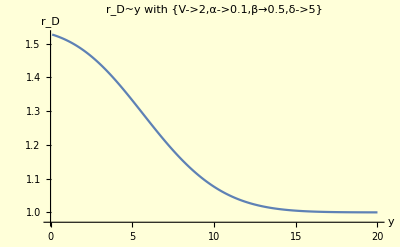

```mathematica
x=Range[200];
ListLinePlot[Transpose[{x/10,ys[[1;;200]]}],AxesLabel->{"y","r_D"},PlotLabel->Style["r_D~y with {V->2,α->0.1,β→0.5,δ->5}",FontSize->18],Background->LightYellow]
```